```mathematica
(* Single funder model *)
Clear[δ] 
H = Exp[-δ*t]*x^{1-η}/(1-η)+ v(r*m-x+ϕ);

(* Control and state variable equations *)
dx= SolveValues[D[H,x]==0,x][[1]]
D[H,m];
vStar = DSolveValue[v'[t]== -r*v[t], v[t], t];

(* Derive optimal amount of money available *)
xStar =  c^(-1/η)Exp[(r-δ)/η*t];
mStar = DSolveValue[{m'[t] == r * m[t]-  xStar+ ϕ, m[0]==B}, m[t],t]//FullSimplify
```

SolveValues::ifun: Inverse functions are being used by SolveValues, so some solutions may not be found; use Reduce for complete solution information.

(ⅇ^(t δ) v)^(-1/η)

B ⅇ^(r t)+(c^(-1/η) (-ⅇ^(r t)+ⅇ^((t (r-δ))/η)) η)/(δ+r (-1+η))+((-1+ⅇ^(r t)) ϕ)/r

```mathematica
(* Use transversality condition to find constant c *)
$Assumptions = B>0 && η>0 && δ>=0 && r>0&& ϕ>=0 && c^(-1/η)∈Reals && r<δ && δ+r (-1+η) > 0;
mInfty = Limit[ mStar * Exp[-r*t], t -> Infinity];
```

```mathematica
cTransverse = ((B + ϕ/r )(δ+r (-1+η))/η)^(-η)
```

(((δ+r (-1+η)) (B+ϕ/r))/η)^-η

```mathematica
(* Deduce money available and spending schedule *)
mS=mStar/. c->cTransverse//FullSimplify
xS= xStar/.c -> cTransverse//FullSimplify
```

(-ϕ+ⅇ^((t (r-δ))/η) (B r+ϕ))/r

(ⅇ^((t (r-δ))/η) (δ+r (-1+η)) (B r+ϕ))/(r η)

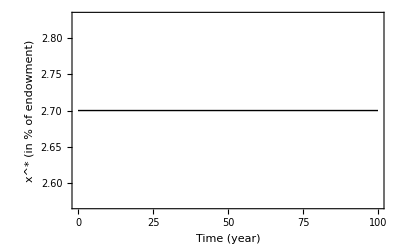

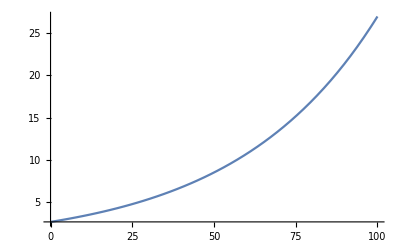

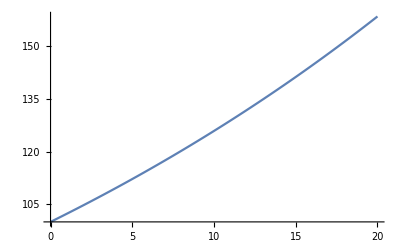

```mathematica
(* Plot money available *)
parameters ={η->2, δ->0.004,r->0.05,ϕ -> 0,B ->100};

(* Optimal spending schedule per endowment *)
Plot[((xS/mS)*100/.parameters), {t,0,100}, Frame->True, FrameLabel->{"Time (year)", " x^* (in % of endowment)"}, LabelStyle->{FontSize->18,FontFamily->"Times", ,Black,Bold}, PlotStyle->{Black,Thick}]

(* Optimal spending schedule per initial endowment *)
Plot[xS/.parameters, {t,0,100}]


(* Money avilable *)
Plot[mS/.parameters, {t,0, 20}]
```

```mathematica
(* Inspect effect of parameters *)
((xS/mS)*100/.B->100/.ϕ->0)
Manipulate[Plot[(100 (δ+r (-1+η)))/η, {t,0,100}],{η,1.1, 10},{ δ,0.001,0.01},{r,0.01,0.08}]
```

(100 (δ+r (-1+η)))/η

```mathematica
spent = NIntegrate[xS/mS/.parameters, {t,0,50} ]
spent*100
```

1.35

135.

```mathematica
(* Suggestion: money available use gliders *)
```